Data

```mathematica
tmpDat=Import["D:\\Users\\jwt\\HFSS\\FromXHN\\simutaneous\\data\\S21_20170224.dat","Data"];
tmpDat2=Import["D:\\Users\\jwt\\HFSS\\FromXHN\\data\\S21_20170224.dat","Data"];
tmpDat3=Import["D:\\Users\\jwt\\HFSS\\FromXHN\\simutaneous\\data\\S21_20170228.dat","Data"];
tmpDat4=Import["D:\\Users\\jwt\\HFSS\\FromXHN\\simutaneous\\data\\S21_20170229.dat","Data"];
```

```mathematica
tmpDat5=Import["D:\\Users\\jwt\\HFSS\\FromXHN\\simutaneous\\data\\S21_20170302.dat","Data"];
```

```mathematica
dat0224=tmpDat[[6;;(Length[tmpDat]-2)]];
dat022402=tmpDat2[[6;;(Length[tmpDat2]-2)]];
dat0228=tmpDat3[[6;;(Length[tmpDat3]-2)]];
dat0229=tmpDat4[[6;;(Length[tmpDat4]-2)]];
```

```mathematica
dat0302=tmpDat5[[6;;(Length[tmpDat5]-2)]];
```

```mathematica
dat0228Sq=Transpose[{dat0228[[;;,1]],dat0228[[;;,2]]^2}];dat0229Sq=Transpose[{dat0229[[;;,1]],dat0229[[;;,2]]^2}];
```

Test FitLorentzian

```mathematica
tmpLor=Table[{x,lorentzianLineShape/.{a->1,x0->2,b->1}},{x,-2,10,0.1}];
```

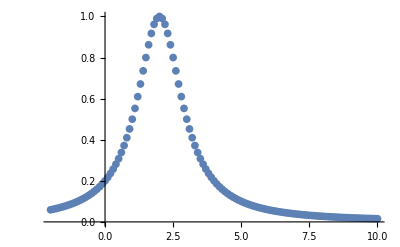

```mathematica
ListPlot[tmpLor]
```

```mathematica
FitLorentzian[tmpLor]
```

Q=2.08511

x_0=1.9994

-Graphics-

Fits

### dat0224

```mathematica
FitLorentzian[dat0224]
```

x_0=35.9533

FWHM=0.065825

Q=546.195

Q_i=672.903

Q_ext=2900.66

-Graphics-

### dat022402

```mathematica
FitLorentzian[dat022402]
```

x_0=36.6239

FWHM=0.127581

Q=287.064

Q_i=335.249

Q_ext=1997.27

-Graphics-

### dat0228

```mathematica
FitLorentzian[dat0228,"Cavity3D"]
```

x_0=37.5565

FWHM=0.265847

Q=141.271

Q_i=163.218

Q_ext=1050.63

-Graphics-

```mathematica
FitLorentzian[dat0228Sq,"Cavity3D"]
```

x_0=37.558

FWHM=0.284992

Q=131.786

Q_i=171.14

Q_ext=573.1

-Graphics-

### dat0229

```mathematica
FitLorentzian[dat0229,"Cavity3D"]
```

x_0=37.5439

FWHM=0.245089

Q=153.185

Q_i=175.65

Q_ext=1197.68

-Graphics-

```mathematica
FitLorentzian[dat0229Sq,"Cavity3D"]
```

x_0=37.5452

FWHM=0.261856

Q=143.381

Q_i=184.024

Q_ext=649.202

-Graphics-

```mathematica
FitLorentzian[dat0228,"Simple2DHanger"]
```

x_0=37.5565

FWHM=0.265847

Q=141.271

Q_i=525.314

Q_ext=193.238

-Graphics-

```mathematica
FitLorentzian[dat0229,"Simple2DHanger"]
```

x_0=37.5439

FWHM=0.245089

Q=153.185

Q_i=598.839

Q_ext=205.839

-Graphics-

### dat0302

```mathematica
FitLorentzian[dat0302,"Cavity3D"]
```

x_0=37.4677

FWHM=0.21619

Q=173.309

Q_i=197.064

Q_ext=1437.71

-Graphics-

```mathematica
FitLorentzian[dat0302,"Simple2DHanger"]
```

x_0=37.4677

FWHM=0.21619

Q=173.309

Q_i=718.854

Q_ext=228.366

-Graphics-